```mathematica
MandelbrotSetPlot[]
```

-Graphics-

```mathematica
DynamicModule[{pts,text,lines},Manipulate[pts=Table[{-Cos[θ],Sin[θ]},{θ,0,2π-(2π)/m,(2π)/m}];
text=Table[Text[ToString[n-1],pts[[n]]1.1],{n,m}];
lines=Line@Table[{pts[[n]],pts[[Mod[(n-1) t,m]+1]]},{n,m}];
Graphics[{{Orange,Circle[]},{Thick,lines},{PointSize[Large],Magenta,Point[pts]},{Pink,text}},ImageSize->Large,PlotRange->1.2],{m,10,100,1},{t,2,52,1}]]
```

```mathematica
DynamicModule[{pts,text,lines},Manipulate[pts=Table[{-Cos[θ],Sin[θ]},{θ,0,2π-(2π)/m,(2π)/m}];
text=Table[Text[ToString[n-1],pts[[n]]1.1],{n,m}];
lines=Line@Table[{pts[[n]],{-Cos[2π Mod[(n-1) t,m]/m],Sin[2π Mod[(n-1) t,m]/m]}},{n,m}];
Graphics[{{Orange,Circle[]},{Thick,ColorData["Rainbow"][0.5Sin[10*2π t/100]+0.5],lines},If[s,{{PointSize[Large],Magenta,Point[pts]},{Pink,text}}]},ImageSize->Large,PlotRange->1.2],{m,10,200,1},{t,0,100,AnimationRate->r},{r,{0.01,0.1,0.5,1}},{{s,True,"点"},{True->"显示",False->"隐藏"}}]]
```

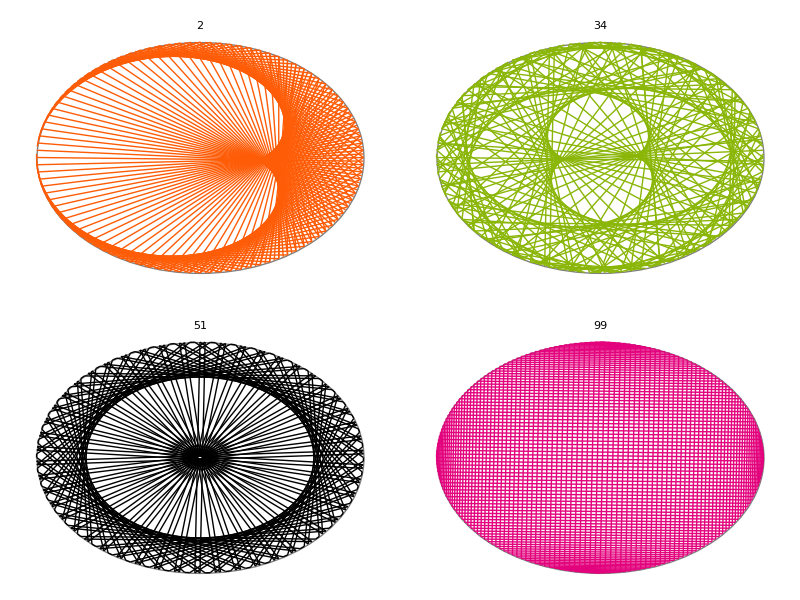

```mathematica
l={2,34,51,99};
m=200;
table=Table[Graphics[{{Gray,Circle[]},{ColorData[3][t],Line@Table[{{-Cos[2π n/m],Sin[2π n/m]},{-Cos[2π Mod[(n-1) t,m]/m],Sin[2π Mod[(n-1) t,m]/m]}},{n,m}]}},PlotLabel->t],
{t,l}];
Grid[Partition[table,2]]
```

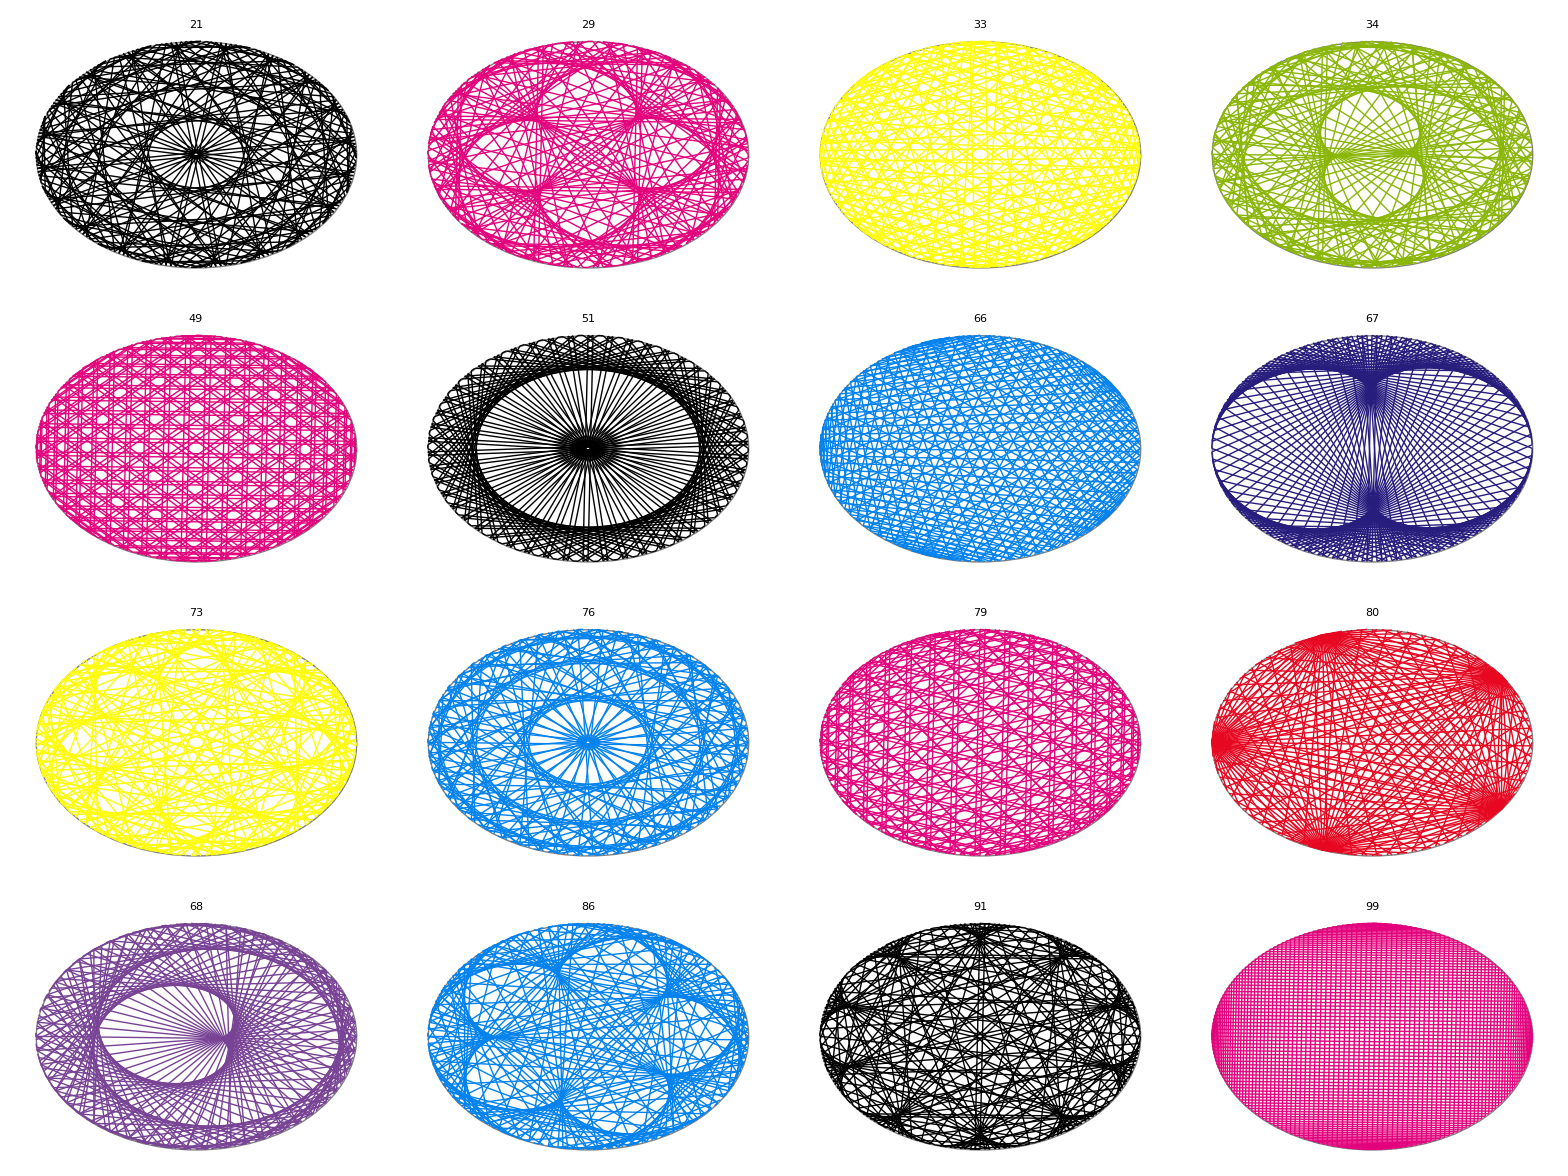

```mathematica
l={21,29,33,34,49,51,66,67,73,76,79,80,68,86,91,99};
m=200;
table=Table[Graphics[{{Gray,Circle[]},{ColorData[3][t],Line@Table[{{-Cos[2π n/m],Sin[2π n/m]},{-Cos[2π Mod[(n-1) t,m]/m],Sin[2π Mod[(n-1) t,m]/m]}},{n,m}]}},PlotLabel->t],
{t,l}];
Grid[Partition[table,4]]
```

### 随机弦

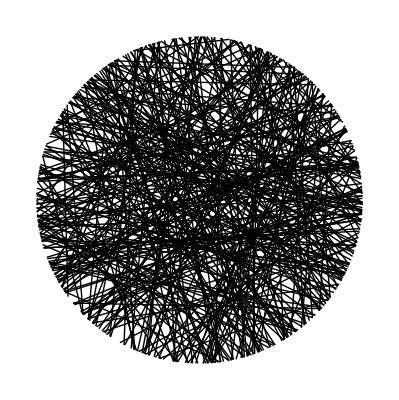

```mathematica
["TwoPointsInCircle",300]//Graphics
```